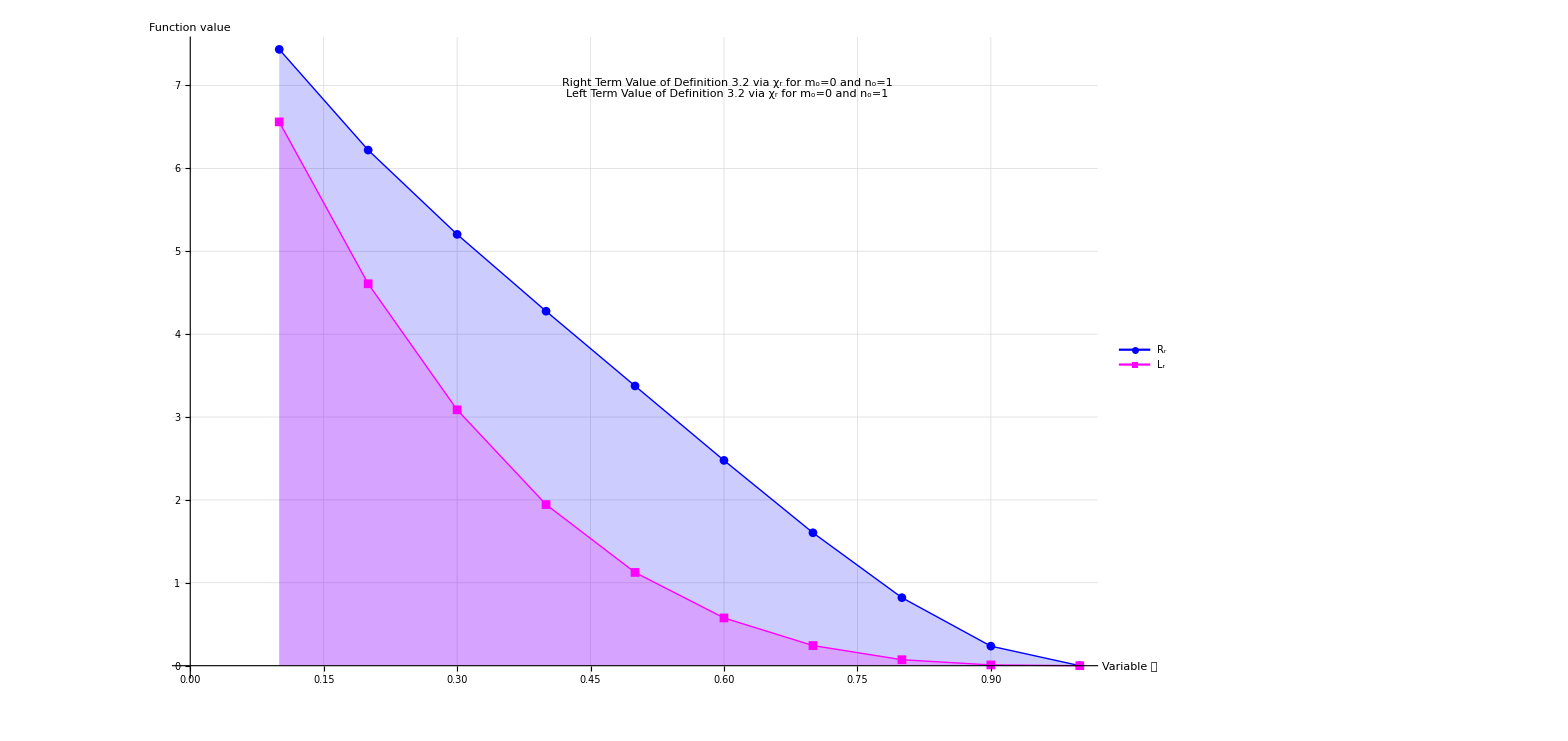

```mathematica
data1={{0.1,7.4358},{0.2,6.2208},{0.3,5.2038},{0.4,4.2768},{0.5,3.375},{0.6,2.4768},{0.7,1.6038},{0.8,0.8208},{0.9,0.2358},{1.0,0.}};
data2={{0.1,6.561},{0.2,4.608},{0.3,3.087},{0.4,1.944},{0.5,1.125},{0.6,0.576},{0.7,0.243},{0.8,0.072},{0.9,0.009},{1.0,0.}};

plot2=ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Magenta,Thick}},PlotLegends->Placed[{Style[Subscript["R","r"],FontSize->40],Style[Subscript["L","r"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["Right Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Blue,28],Style["Left Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Magenta,28]}],RoundingRadius->5],Scaled[{0.6,0.92}]]]
```

```mathematica
Table[(2t+3(0.5)(1-t))(1+(2t+3(0.5)(1-t))),{t,0,1,0.1}]
```

{3.75,3.9525,4.16,4.3725,4.59,4.8125,5.04,5.2725,5.51,5.7525,6.}

```mathematica
Table[t(2(3)-((1-t)(1+(1-t))))+0.5(1-t) (12-((t)(1+(t)))),{t,0,1,0.1}]
```

{6.,5.7795,5.616,5.5065,5.448,5.4375,5.472,5.5485,5.664,5.8155,6.}

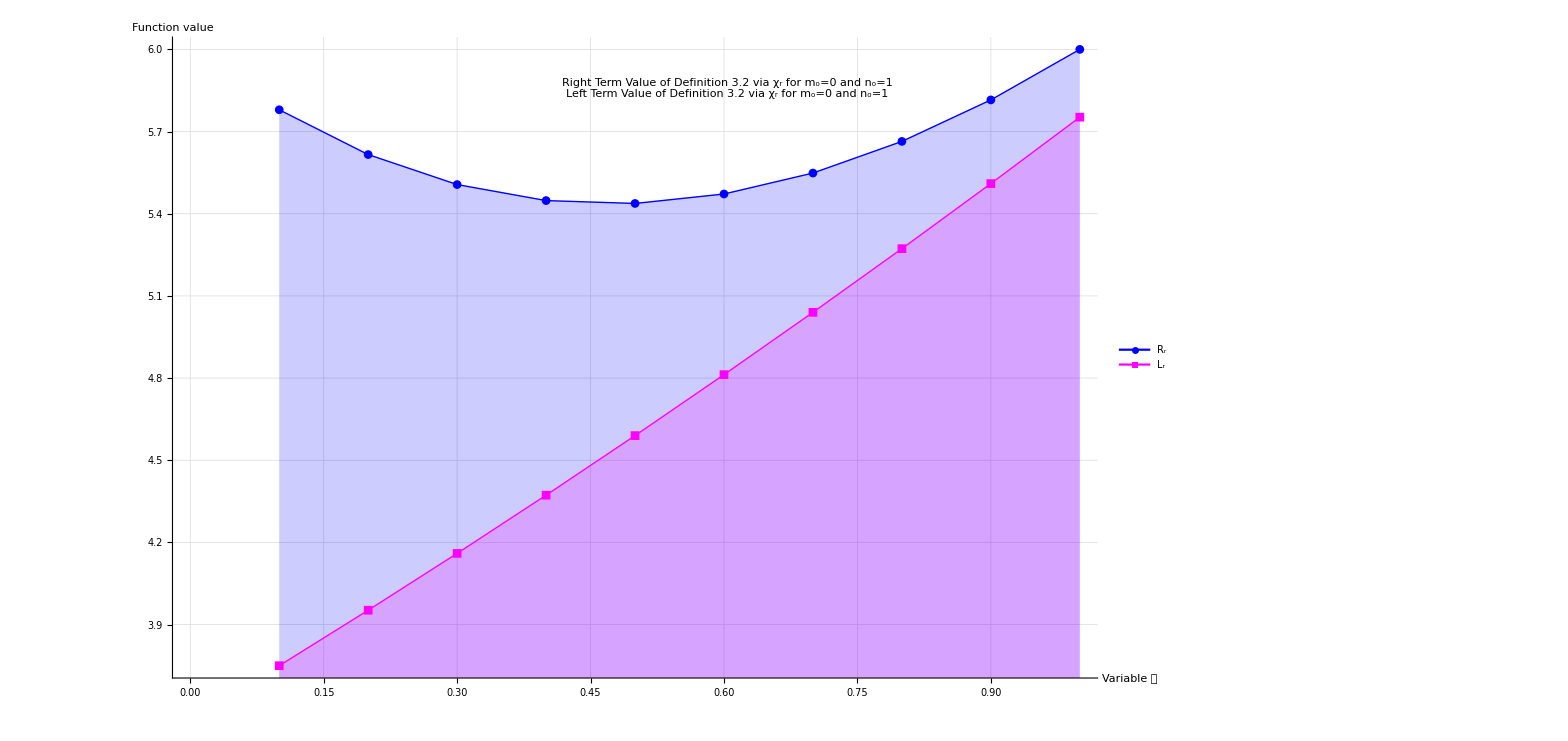

```mathematica
data1={{0.1,5.7795000000000005},{0.2,5.616},{0.3,5.5065},{0.4,5.448},{0.5,5.4375},{0.6,5.4719999999999995},{0.7,5.548500000000001},{0.8,5.664},{0.9,5.8155},{1.0,6.}};
data2={{0.1,3.75},{0.2,3.9524999999999997},{0.3,4.16},{0.4,4.3725},{0.5,4.59},{0.6,4.8125},{0.7,5.04},{0.8,5.272500000000001},{0.9,5.51},{1.0,5.7525}};

plot2=ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Magenta,Thick}},PlotLegends->Placed[{Style[Subscript["R","r"],FontSize->40],Style[Subscript["L","r"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["Right Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Blue,28],Style["Left Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Magenta,28]}],RoundingRadius->5],Scaled[{0.6,0.92}]]]
```

```mathematica
Table[(2t+3(0.1)(1-t))(1+(2t+3(0.1)(1-t))),{t,0,1,0.1}]
```

{0.39,0.6909,1.0496,1.4661,1.9404,2.4725,3.0624,3.7101,4.4156,5.1789,6.}

```mathematica
Table[t(2(3)-((1-t)(1+(1-t))))+0.1(1-t) (12-((t)(1+(t)))),{t,0,1,0.1}]
```

{1.2,1.4991,1.8528,2.2557,2.7024,3.1875,3.7056,4.2513,4.8192,5.4039,6.}

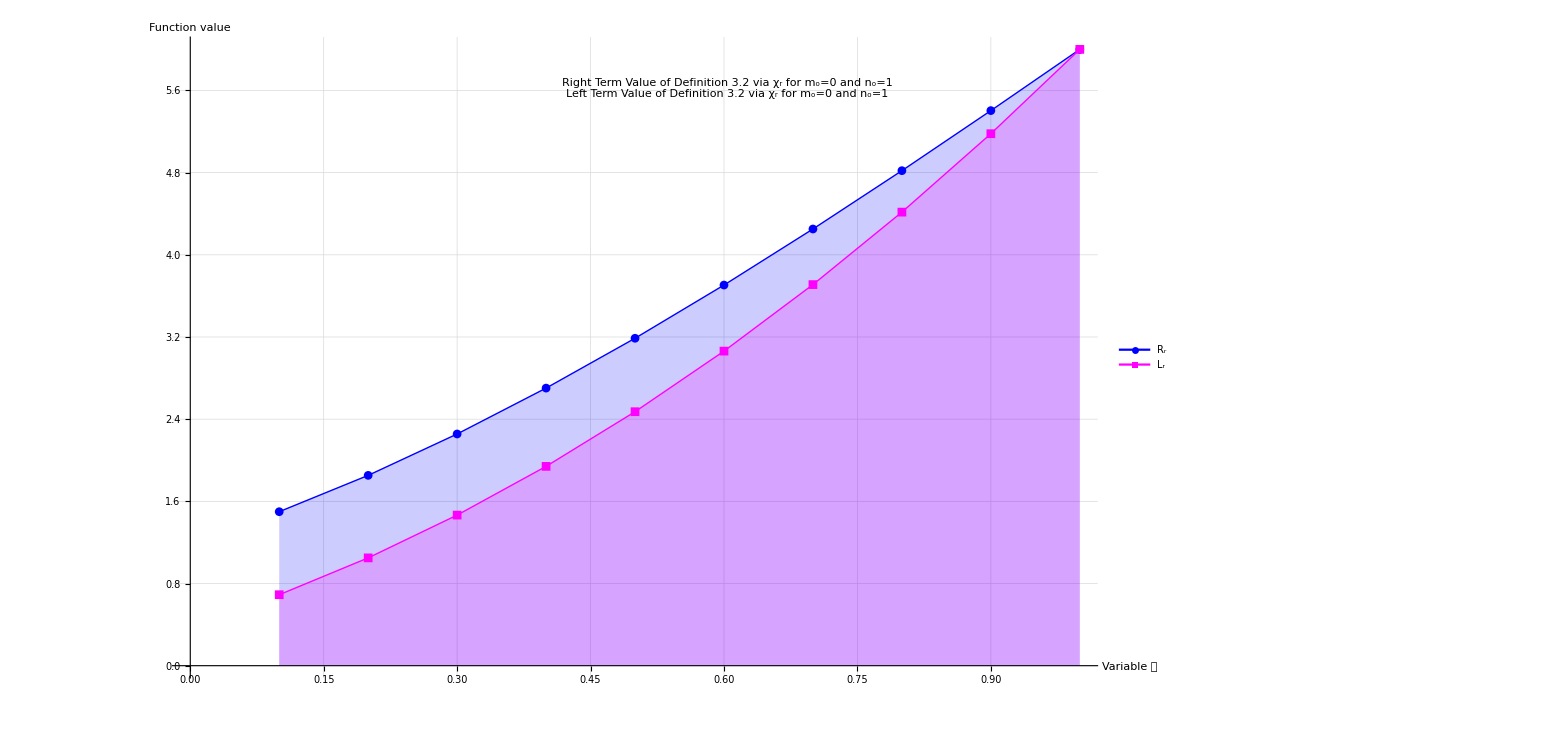

```mathematica
data1={{0.1,1.4991000000000003},{0.2,1.8528000000000002},{0.3,2.2557},{0.4,2.7024},{0.5,3.1875},{0.6,3.7056000000000004},{0.7,4.2513000000000005},{0.8,4.8191999999999995},{0.9,5.4039},{1.0,6.}};
data2={{0.1,0.6909000000000002},{0.2,1.0496000000000003},{0.3,1.4661000000000002},{0.4,1.9404000000000001},{0.5,2.4724999999999997},{0.6,3.062400000000001},{0.7,3.710100000000001},{0.8,4.4156},{0.9,5.1789000000000005},{1.0,6.}};
plot2=ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Magenta,Thick}},PlotLegends->Placed[{Style[Subscript["R","r"],FontSize->40],Style[Subscript["L","r"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["Right Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Blue,28],Style["Left Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Magenta,28]}],RoundingRadius->5],Scaled[{0.6,0.92}]]]
```

```mathematica
Table[(2t+3(0.3)(1-t))(1+(2t+3(0.3)(1-t))),{t,0.1,1,0.1}]
```

{2.0301,2.3744,2.7429,3.1356,3.5525,3.9936,4.4589,4.9484,5.4621,6.}

```mathematica
Table[t(2(3)-((1-t)(1+(1-t))))+0.3(1-t) (12-((t)(1+(t)))),{t,0.1,1,0.1}]
```

{3.6393,3.7344,3.8811,4.0752,4.3125,4.5888,4.8999,5.2416,5.6097,6.}

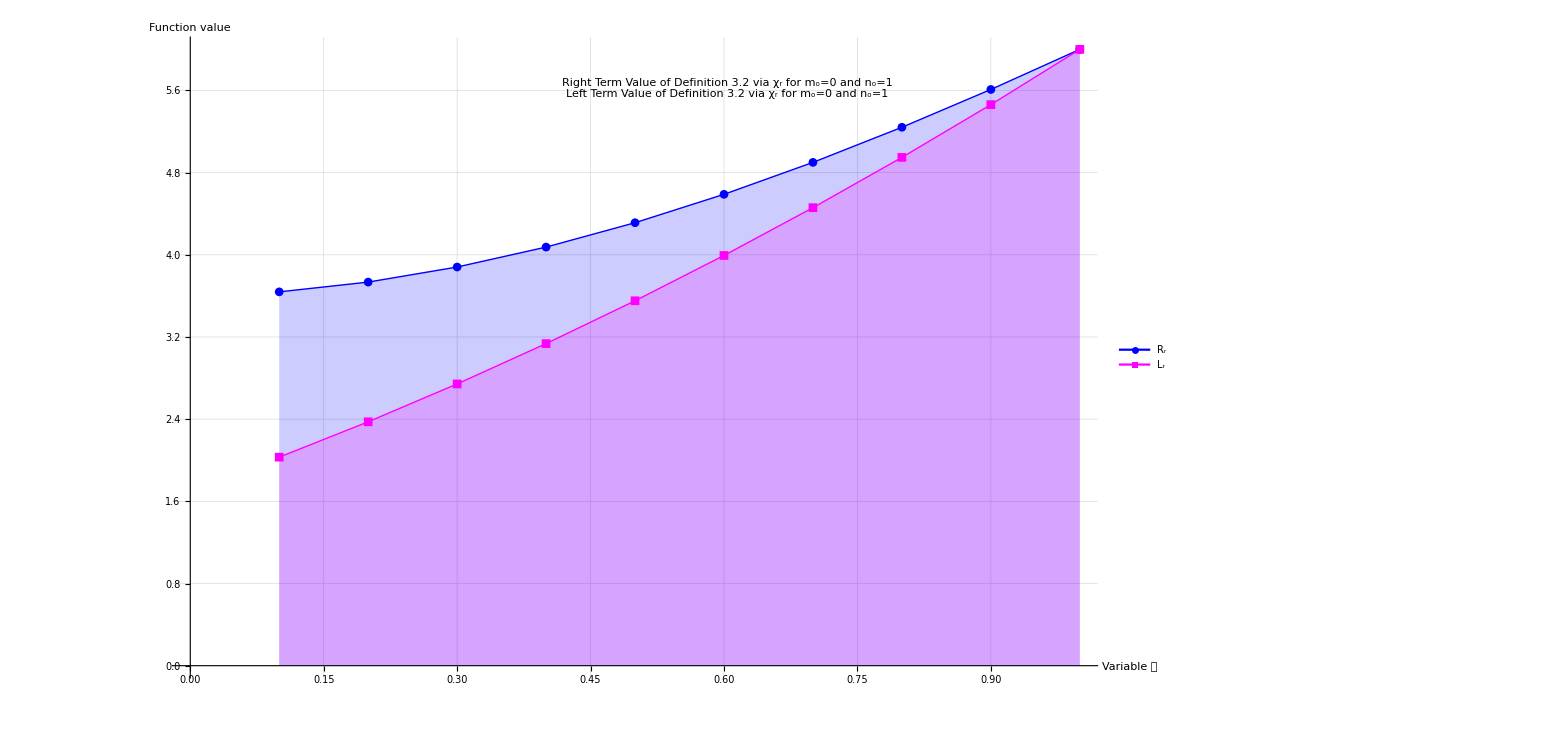

```mathematica
data1={{0.1,3.6393000000000004},{0.2,3.7344},{0.3,3.8811},{0.4,4.0752},{0.5,4.3125},{0.6,4.5888},{0.7,4.899900000000001},{0.8,5.241599999999999},{0.9,5.6097},{1.0,6.}};
data2={{0.1,2.0301},{0.2,2.3744000000000005},{0.3,2.7429},{0.4,3.1355999999999993},{0.5,3.5525},{0.6,3.9936000000000003},{0.7,4.4589},{0.8,4.9484},{0.9,5.4621},{1.0,6.}};
plot2=ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Magenta,Thick}},PlotLegends->Placed[{Style[Subscript["R","r"],FontSize->40],Style[Subscript["L","r"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["Right Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Blue,28],Style["Left Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Magenta,28]}],RoundingRadius->5],Scaled[{0.6,0.92}]]]
```

```mathematica
Table[(2t+3(0.7)(1-t))(1+(2t+3(0.7)(1-t))),{t,0.1,1,0.1}]
```

{6.4581,6.4064,6.3549,6.3036,6.2525,6.2016,6.1509,6.1004,6.0501,6.}

```mathematica
Table[t(2(3)-((1-t)(1+(1-t))))+0.7(1-t) (12-((t)(1+(t)))),{t,0.1,1,0.1}]
```

{7.9197,7.4976,7.1319,6.8208,6.5625,6.3552,6.1971,6.0864,6.0213,6.}

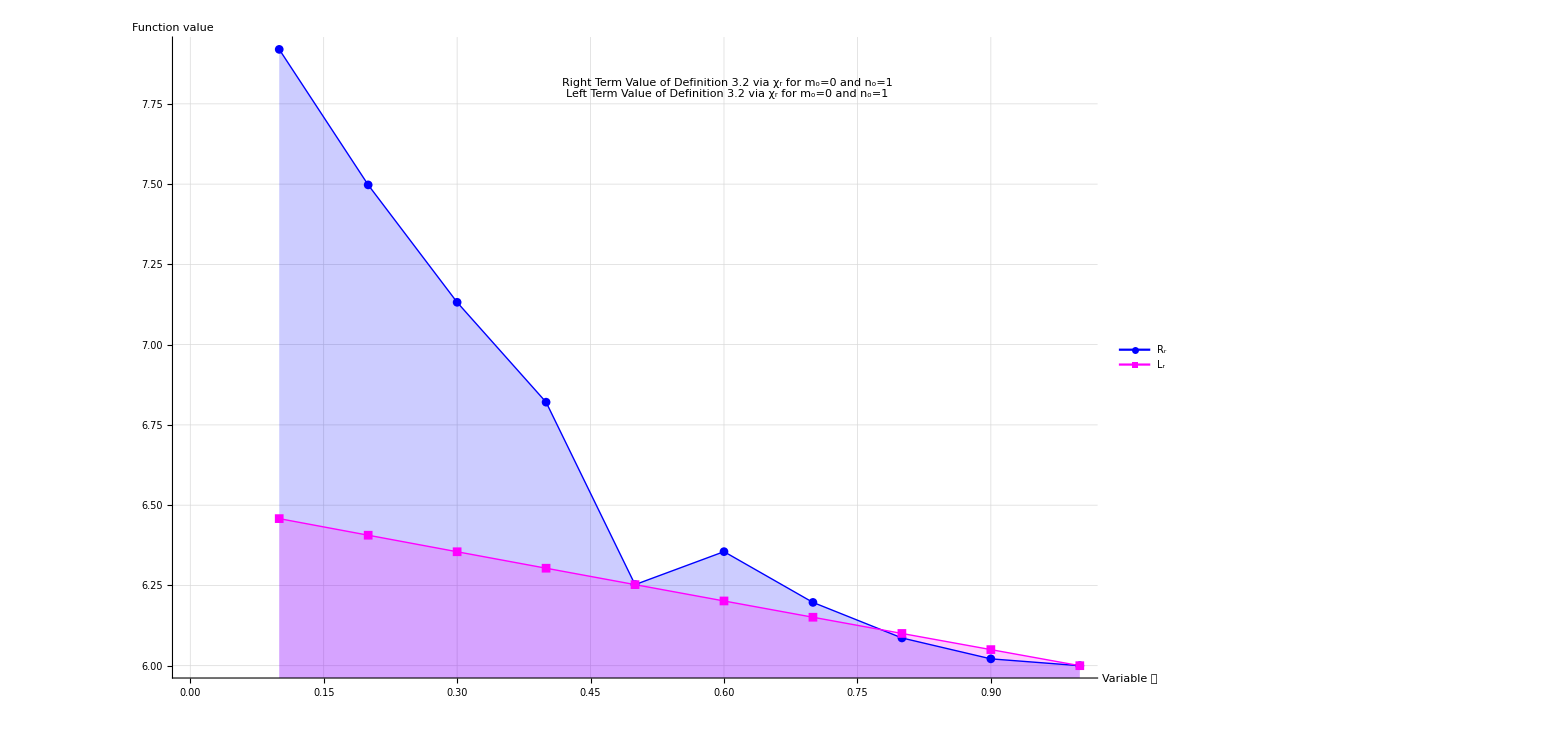

```mathematica
data1={{0.1,7.919700000000001},{0.2,7.497599999999999},{0.3,7.1319},{0.4,6.820799999999999},{0.5,6.2524999999999995},{0.6,6.3552},{0.7,6.1971},{0.8,6.086399999999999},{0.9,6.0213},{1.0,6.}};
data2={{0.1,6.458099999999999},{0.2,6.406399999999998},{0.3,6.354899999999999},{0.4,6.303599999999998},{0.5,6.2524999999999995},{0.6,6.2016},{0.7,6.150899999999999},{0.8,6.1004000000000005},{0.9,6.050099999999999},{1.0,6.}};
plot2=ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Blue,Thick},{Magenta,Thick}},PlotLegends->Placed[{Style[Subscript["R","r"],FontSize->40],Style[Subscript["L","r"],FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["Right Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Blue,28],Style["Left Term Value of Definition 3.2 via \!\(\*SubscriptBox[\(χ\), \(r\)]\) for \!\(\*SubscriptBox[\(m\), \(o\)]\)=0 and \!\(\*SubscriptBox[\(n\), \(o\)]\)=1",Magenta,28]}],RoundingRadius->5],Scaled[{0.6,0.92}]]]
```

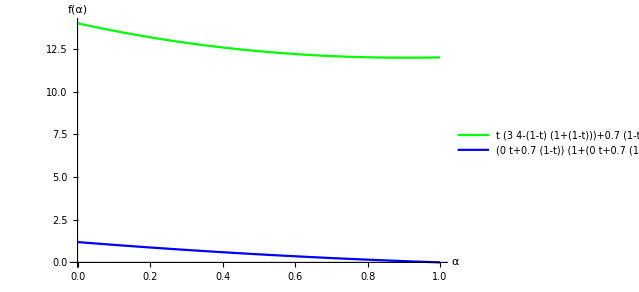

```mathematica
Plot[{t(3(4)-((1-t)(1+(1-t))))+0.7(1-t) (20-((t)(1+(t)))),(0t+1(0.7)(1-t))(1+(0t+1(0.7)(1-t)))},{t,0,1},ImageSize -> {473., Automatic},PlotStyle->{Green,Blue,Red},Mesh->None,Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},AxesLabel->{Style["α",15,Bold,Red],Style["f(α)",15,Bold,Red]},Axes->True,PlotLegends->"Expressions"]
```

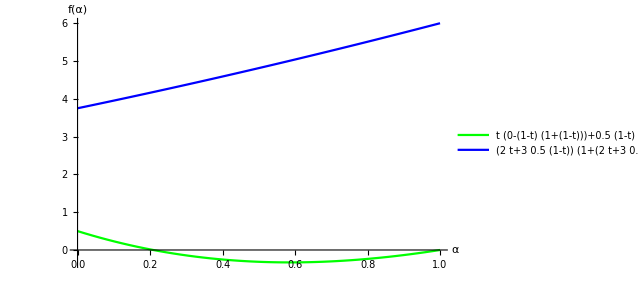

```mathematica
Plot[{t(0-((1-t)(1+(1-t))))+0.5(1-t) (1-((t)(1+(t)))),(2t+3(0.5)(1-t))(1+(2t+3(0.5)(1-t)))},{t,0,1},ImageSize -> {473., Automatic},PlotStyle->{Green,Blue,Red},Mesh->None,Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},AxesLabel->{Style["α",15,Bold,Red],Style["f(α)",15,Bold,Red]},Axes->True,PlotLegends->"Expressions"]
```

```mathematica
Plot3D[{t(0-((1-t)(1+(1-t))))+m(1-t) (1-((t)(1+(t)))),((0)t+1(m)(1-t))(1+((0)t+1(m)(1-t)))},{m,0.5,1},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(2(3)-((1-t)(1+(1-t))))+m(1-t) (3(4)-((t)(1+(t)))),(2t+3(m)(1-t))(1+(2t+3(m)(1-t)))},{m,0,0.6},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(2(3)-((1-t)(1+(1-t))))+m(1-t) (5(6)-((t)(1+(t)))),(2t+5(m)(1-t))(1+(2t+5(m)(1-t)))},{m,0,1},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(3(4)-((1-t)(1+(1-t))))+m(1-t) (4(5)-((t)(1+(t)))),(3t+4(m)(1-t))(1+(3t+4(m)(1-t)))},{m,0,0.8},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(4(5)-((1-t)(1+(1-t))))+m(1-t) (5(6)-((t)(1+(t)))),(4t+5(m)(1-t))(1+(4t+5(m)(1-t)))},{m,0,0.9},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(5(6)-((1-t)(1+(1-t))))+m(1-t) (6(7)-((t)(1+(t)))),(5t+6(m)(1-t))(1+(5t+6(m)(1-t)))},{m,0,0.9},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(6(7)-((1-t)(1+(1-t))))+m(1-t) (7(8)-((t)(1+(t)))),(6t+7(m)(1-t))(1+(6t+7(m)(1-t)))},{m,0,1},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(7(8)-((1-t)(1+(1-t))))+m(1-t) (8(9)-((t)(1+(t)))),(7t+8(m)(1-t))(1+(7t+8(m)(1-t)))},{m,0,0.9},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(9(10)-((1-t)(1+(1-t))))+m(1-t) (10(11)-((t)(1+(t)))),(9t+10(m)(1-t))(1+(9t+10(m)(1-t)))},{m,0,1},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(12(13)-((1-t)(1+(1-t))))+m(1-t) (13(14)-((t)(1+(t)))),(12t+13(m)(1-t))(1+(12t+13(m)(1-t)))},{m,0,0.9},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{0.7(a(1+a)-(((1-0.7)(b-a))(1+(1-0.7)(b-a))))+0.8(1-0.7) (b(1+b)-((0.7(b-a))(1+(0.7)(b-a)))),(a(0.7)+b(0.8)(1-0.7))(1+(a(0.7)+b(0.8)(1-0.7)))},{a,5,6},{b,7,8},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Plot3D[{t(5(6)-((1-t)(1+(1-t))))+m(1-t) (6(7)-((t)(1+(t)))),(5t+6(m)(1-t))(1+(5t+6(m)(1-t)))},{m,0,0.9},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Red,Yellow},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],AxesLabel->{Style["a",15,Bold,Red],Style["b",15,Bold,Red],Style["f(a,b)",15,Bold,Red]},Axes->True,PlotLegends->Placed[{"Right Term","Left Term"},{0.1,0.1}]]
```

-Graphics-

```mathematica
Table[(5t+6(0.3)(1-t))(1+(5t+6(0.3)(1-t))),{t,0.1,1,0.1}]
```

{6.6144,8.3936,10.3776,12.5664,14.96,17.5584,20.3616,23.3696,26.5824,30.}

```mathematica
Table[t(5(6)-((1-t)(1+(1-t))))+0.3(1-t) (6(7)-((t)(1+(t)))),{t,0.1,1,0.1}]
```

{14.1393,15.7344,17.3811,19.0752,20.8125,22.5888,24.3999,26.2416,28.1097,30.}

```mathematica
data1={{0.1,14.139300000000002},{0.2,15.734399999999999},{0.3,17.3811},{0.4,19.0752},{0.5,20.8125},{0.6,22.5888},{0.7,24.3999},{0.8,26.241600000000002},{0.9,28.1097},{1.0,30.}};
data2={{0.1,6.614400000000001},{0.2,8.3936},{0.3,10.3776},{0.4,12.5664},{0.5,14.96},{0.6,17.5584},{0.7,20.3616},{0.8,23.369599999999995},{0.9,26.582399999999996},{1.0,30.}};
plot2=ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Orange,Thick},{Black,Thick}},PlotLegends->Placed[{Style["R",FontSize->40],Style["L",FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable 𝔅",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["m=0.3",Black,28],Style["𝔅ϵ[0, 1]",Black,28]}],RoundingRadius->5],Scaled[{0.1,0.92}]]]
```

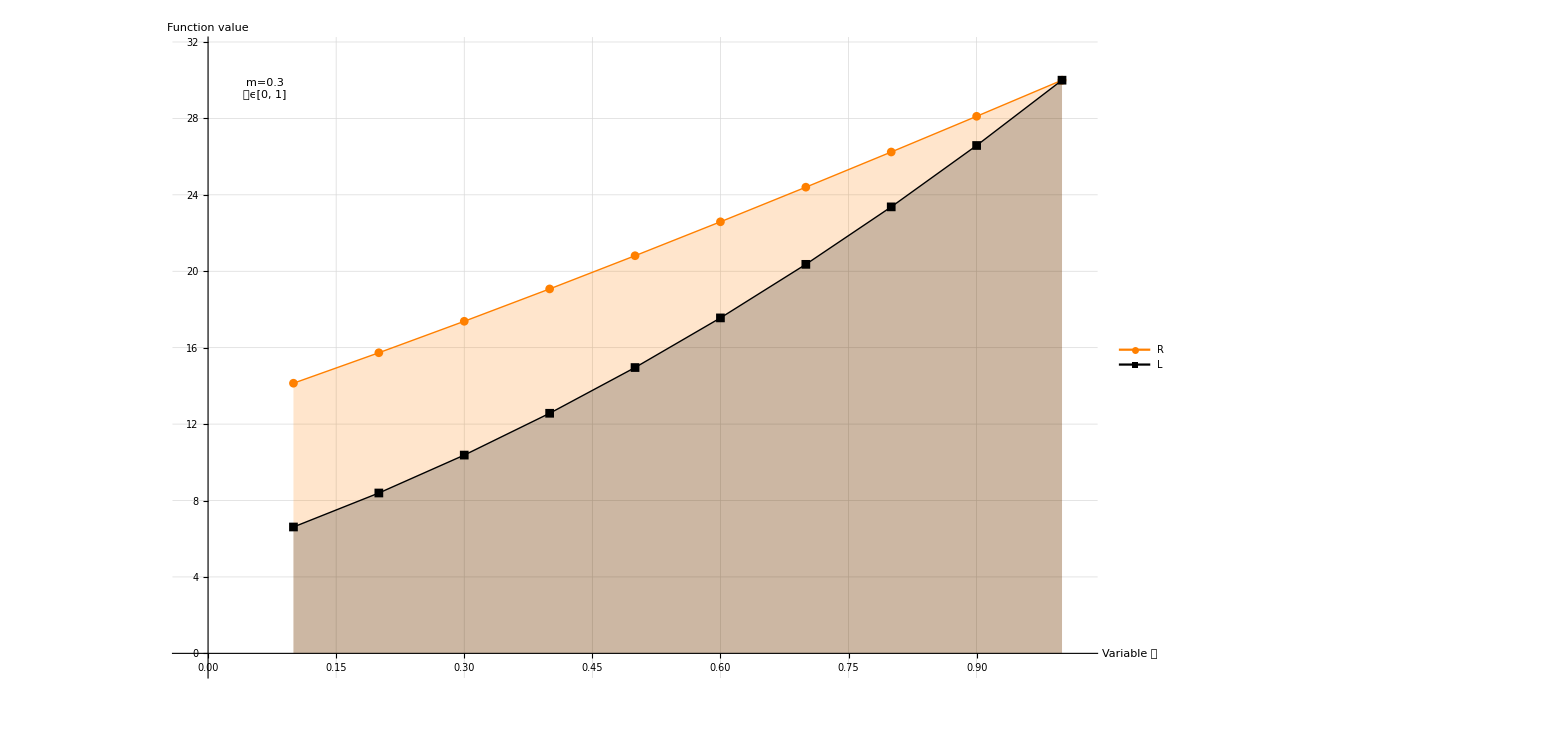

```mathematica
Table[(5(0.5)+6(m)(1-0.5))(1+(5(0.5)+6(m)(1-0.5))),{m,0,0.9,0.1}]
```

{8.75,10.64,12.71,14.96,17.39,20.,22.79,25.76,28.91,32.24}

```mathematica
Table[0.5(5(6)-((1-0.5)(1+(1-0.5))))+m(1-0.5) (6(7)-((0.5)(1+(0.5)))),{m,0,0.9,0.1}]
```

{14.625,16.6875,18.75,20.8125,22.875,24.9375,27.,29.0625,31.125,33.1875}

```mathematica
data1={{0.1,14.625},{0.2,16.6875},{0.3,18.75},{0.4,20.8125},{0.5,22.875},{0.6,24.9375},{0.7,27.},{0.8,29.0625},{0.9,31.125},{1, 33.1875}};
data2={{0.1,8.75},{0.2,10.639999999999999},{0.3,12.709999999999999},{0.4,14.960000000000003},{0.5,17.39},{0.6,20.},{0.7,22.790000000000006},{0.8,25.759999999999998},{0.9,28.910000000000004},{1.0,32.24}};
plot2=ListLinePlot[{data1,data2},PlotMarkers->Automatic,PlotStyle->{{Orange,Thick},{Black,Thick}},PlotLegends->Placed[{Style["R",FontSize->40],Style["L",FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable m",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["𝔅=0.5",Black,28],Style["mϵ[0, 1)",Black,28]}],RoundingRadius->5],Scaled[{0.1,0.92}]]]
```

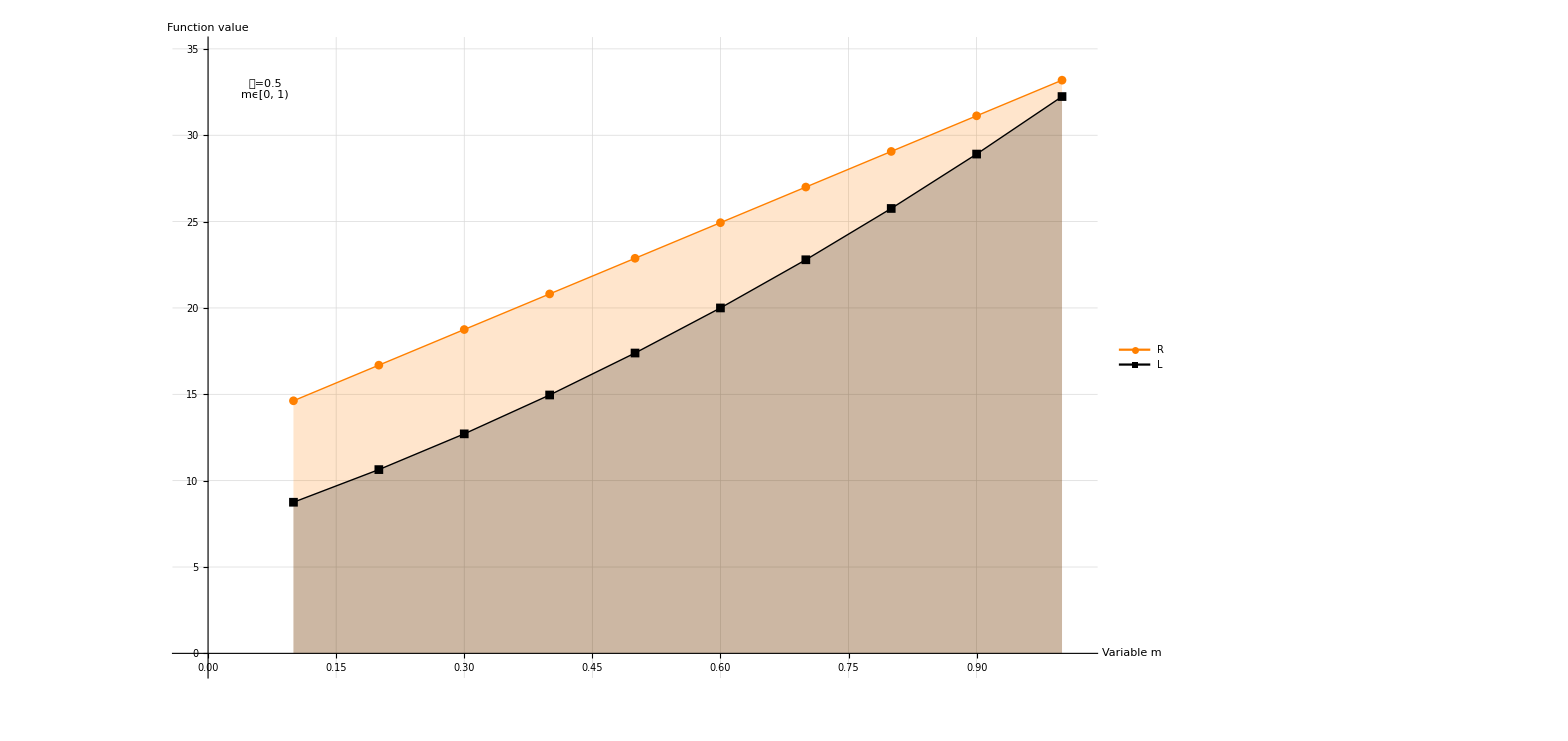

```mathematica
Plot3D[{t(5(6)-((1-t)(1+(1-t))))+m(1-t) (6(7)-((t)(1+(t)))),(5t+6(m)(1-t))(1+(5t+6(m)(1-t)))},{m,0,0.9},{t,0,1},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Orange,Black},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],Axes->True,PlotLegends->Placed[{Style["R"],Style["L"]},{0.9,0.9}]]
```

```mathematica
Plot3D[{0.7(a(1+a)-(((1-0.7)(b-a))(1+(1-0.7)(b-a))))+0.8(1-0.7) (b(1+b)-((0.7(b-a))(1+(0.7)(b-a)))),(a(0.7)+b(0.8)(1-0.7))(1+(a(0.7)+b(0.8)(1-0.7)))},{a,5,6},{b,7,8},ImageSize -> {473., Automatic},Ticks->{Automatic,Automatic,Automatic}, PlotRange ->Automatic,LabelStyle->{FontSize->13.5,Bold},Boxed->False,FaceGrids->{{0,0,-1},{0,1,0},{1,0,0}},PlotStyle->{Orange,Black},ViewPoint->{-1.963961,-1.03555567,0.70428},PlotStyle->Opacity[5],Axes->True,PlotLegends->Placed[{Style["R"],Style["L"]},{0.9,0.9}]]
```

```mathematica
Integrate[(1+m)(11-(1+m)x)/(2m),{x,5,5.5}]
```

0.125+1.4375/m-1.3125 m

```mathematica
Integrate[0.5(x(1+x)+m((x/m)(1+(x/m)))),{x,5,6}]
```

20.6667+15.1667/m

```mathematica
Integrate[0.5((6-x)((((x-5)(6-5m))/m)(1+(((x-5)(6-5m))/m)))+m(x-5)(((((6-x)(6-5m))/m)(1+(((6-x)(6-5m))/m))))+m(x-5)(((((6-x)(6-5m))/m^2)(1+(((6-x)(6-5m))/m^2))))+m^2(6-x)(((((x-5)(6-5m))/m^2)(1+(((x-5)(6-5m))/m^2))))),{x,5,6}]
```

-0.25+1.5/m^3+0.5/m^2-1.45833/m+0.208333 m

```mathematica
Table[(5.5)(6.5)+0.125+(1.4375/m)-1.3125m,{m,0.2,0.9,0.1}]
```

{42.8,40.2729,38.9438,38.0938,37.4833,37.0098,36.6219,36.291}

```mathematica
Table[20.6667+(15.1667/m),{m,0.2,0.9,0.1}]
```

{96.5002,71.2224,58.5835,51.0001,45.9445,42.3334,39.6251,37.5186}

```mathematica
Table[(1/4)(30+6(1+6/m)+5(1+5/m)+6(1+6/m^2))+0.25-(1.5/m^3)-(0.5/m^2)+(1.45833/m)+0.208333m,{m,0.2,0.9,0.1}]
```

{120.583,106.646,83.5417,67.5208,56.6389,48.9886,43.4036,39.1885}

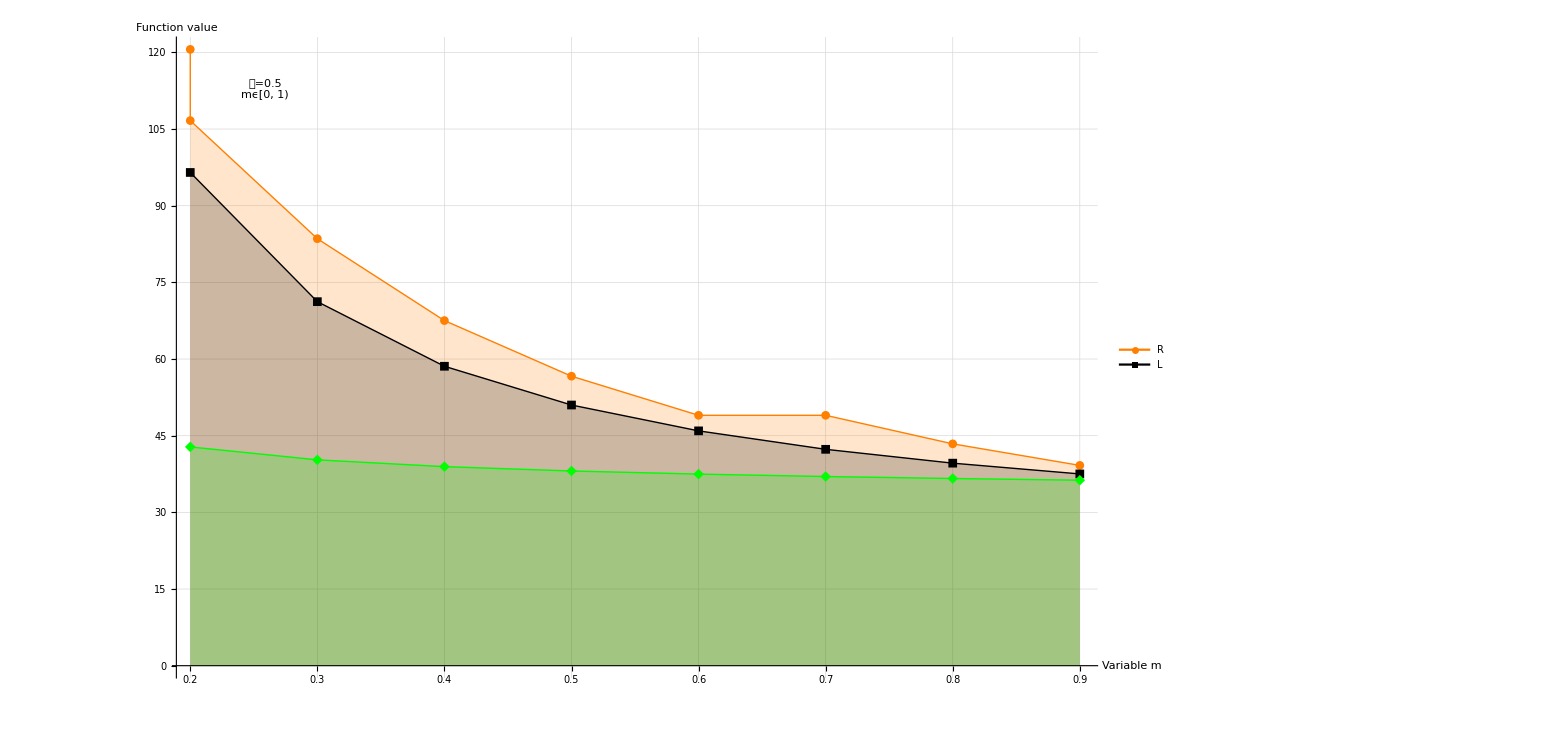

```mathematica
data1={{0.2,120.5833166},{0.2,106.64582212222221},{0.3,83.5416582},{0.4,67.5208265},{0.5,56.63888313333332},{0.6,48.98863689008747},{0.7,48.98863689008747},{0.8,43.4036414},{0.9,39.18852480288065}};
data2={{0.2,96.5002},{0.3,71.22236666666666},{0.4,58.58345},{0.5,51.0001},{0.6,45.94453333333333},{0.7,42.333414285714284},{0.8,39.625074999999995},{0.9,37.518588888888885}};
data3={{0.2,42.8},{0.3,40.27291666666667},{0.4,38.94375},{0.5,38.09375},{0.6,37.483333333333334},{0.7,37.00982142857143},{0.8,36.621875},{0.9,36.29097222222222}};
plot2=ListLinePlot[{data1,data2,data3},PlotMarkers->Automatic,PlotStyle->{{Orange,Thick},{Black,Thick}, {Green,Thick}},PlotLegends->Placed[{Style["R",FontSize->40],Style["L",FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable m",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["𝔅=0.5",Black,28],Style["mϵ[0, 1)",Black,28]}],RoundingRadius->5],Scaled[{0.1,0.92}]]]
```

```mathematica
Plot[{(1/4)(30+6(1+6/m)+5(1+5/m)+6(1+6/m^2))+0.25-(1.5/m^3)-(0.5/m^2)+(1.45833/m)+0.208333m,20.6667+(15.1667/m),(5.5)(6.5)+0.125+(1.4375/m)-1.3125m},{m,0.2,0.9},PlotStyle->{{Orange,Thick},{Black,Thick}, {Green,Thick}},PlotLegends->Placed[{Style["R",FontSize->40],Style["M",FontSize->40],Style["L",FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable m",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["mϵ(0.2, 0.9)",Black,28]}],RoundingRadius->5],Scaled[{0.9,0.9}]]]
```

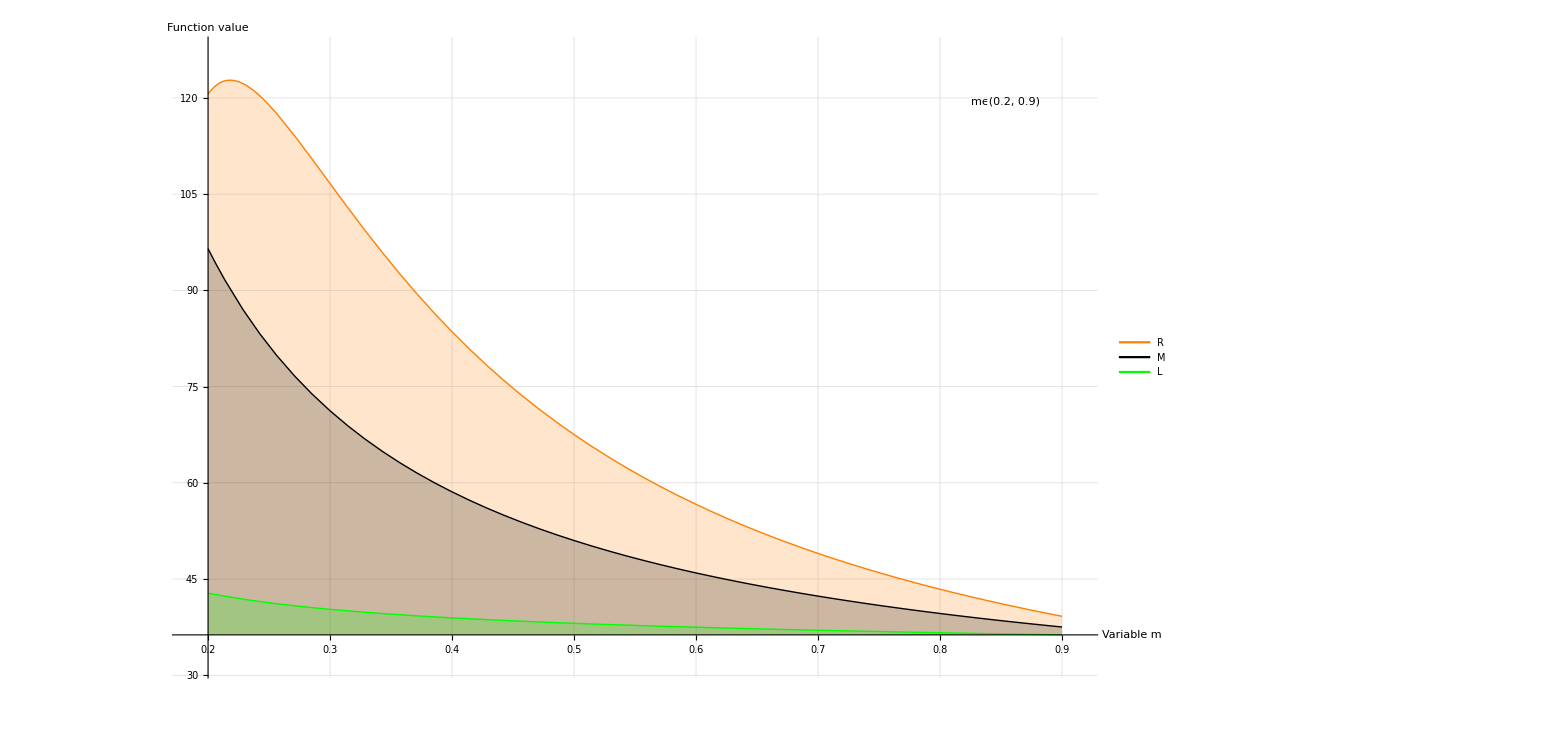

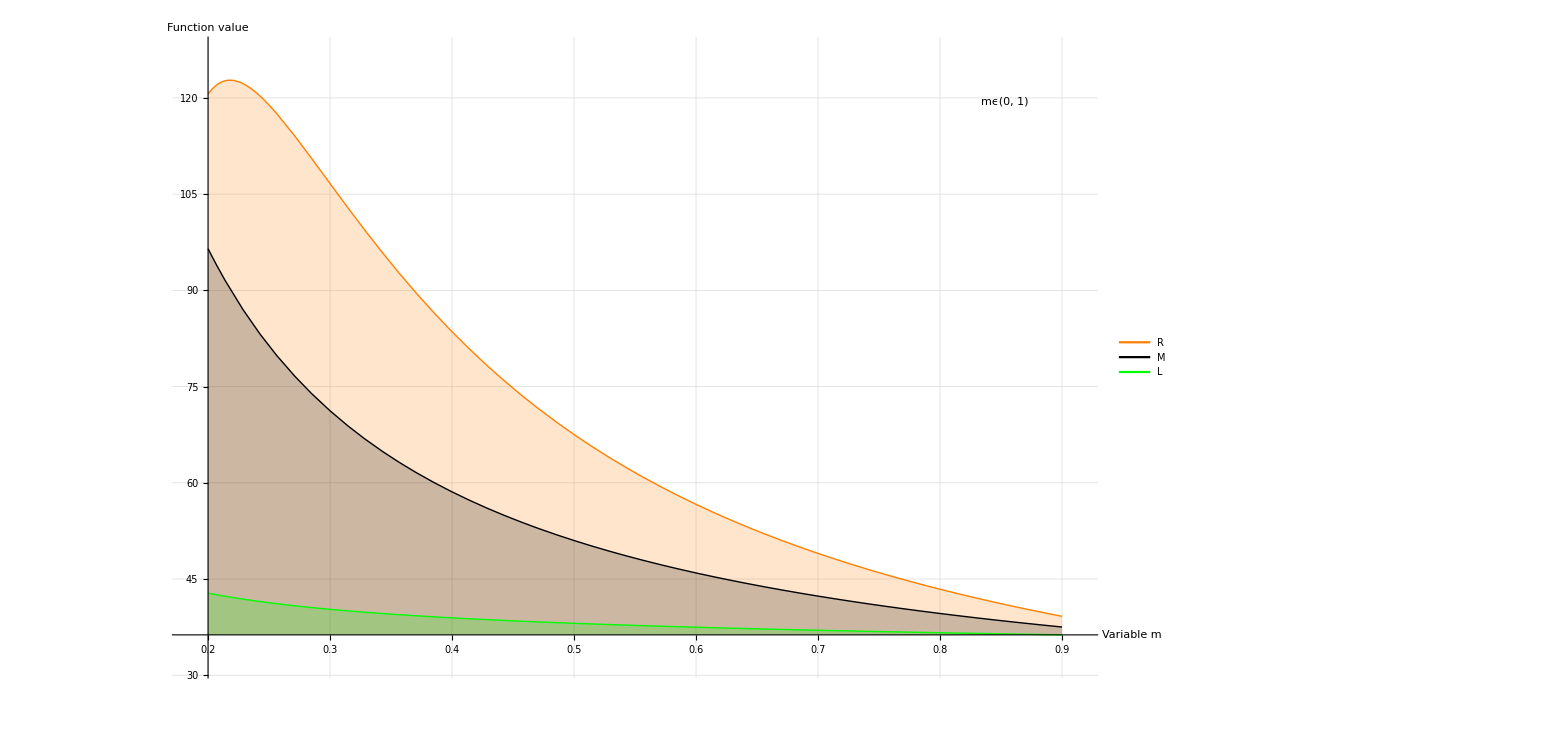

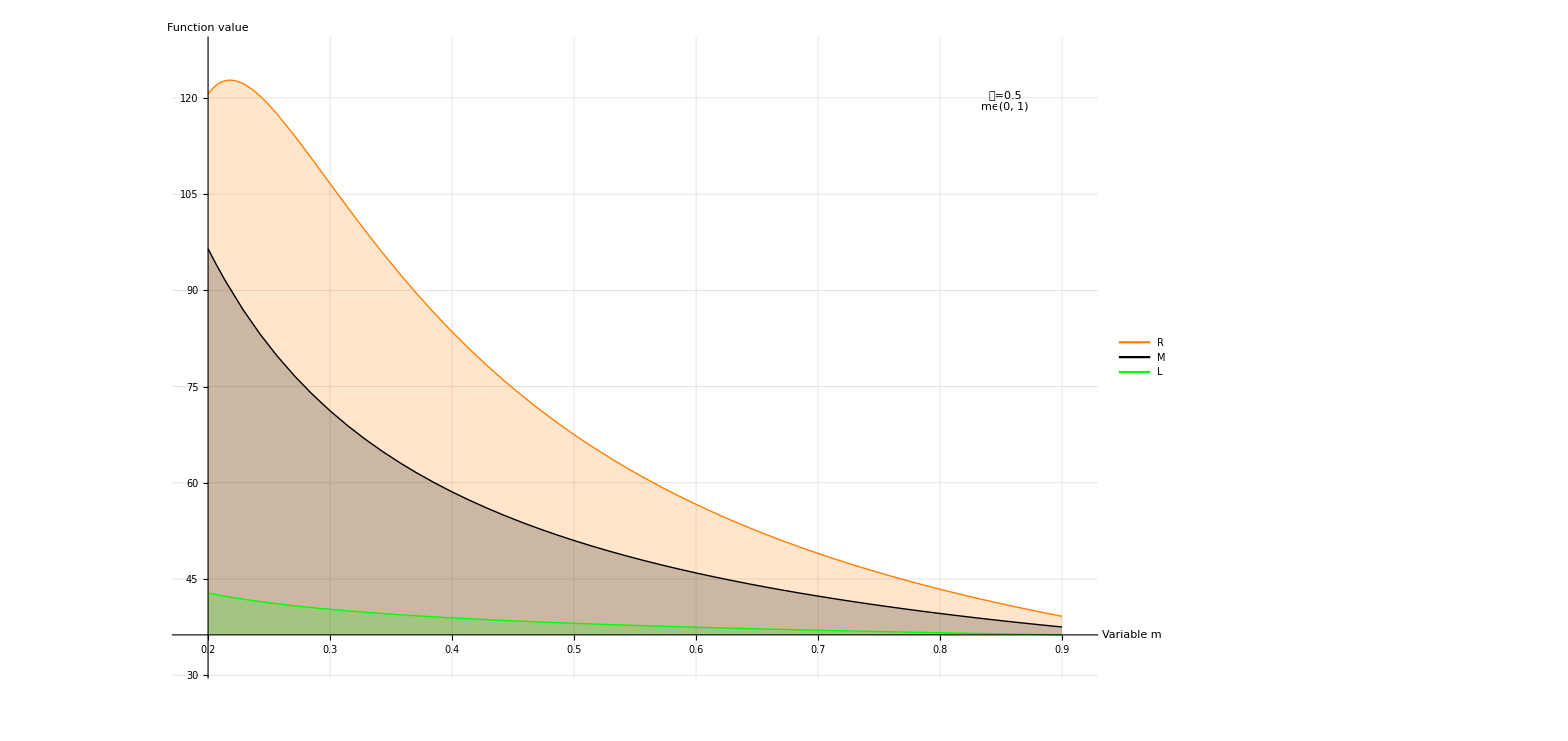

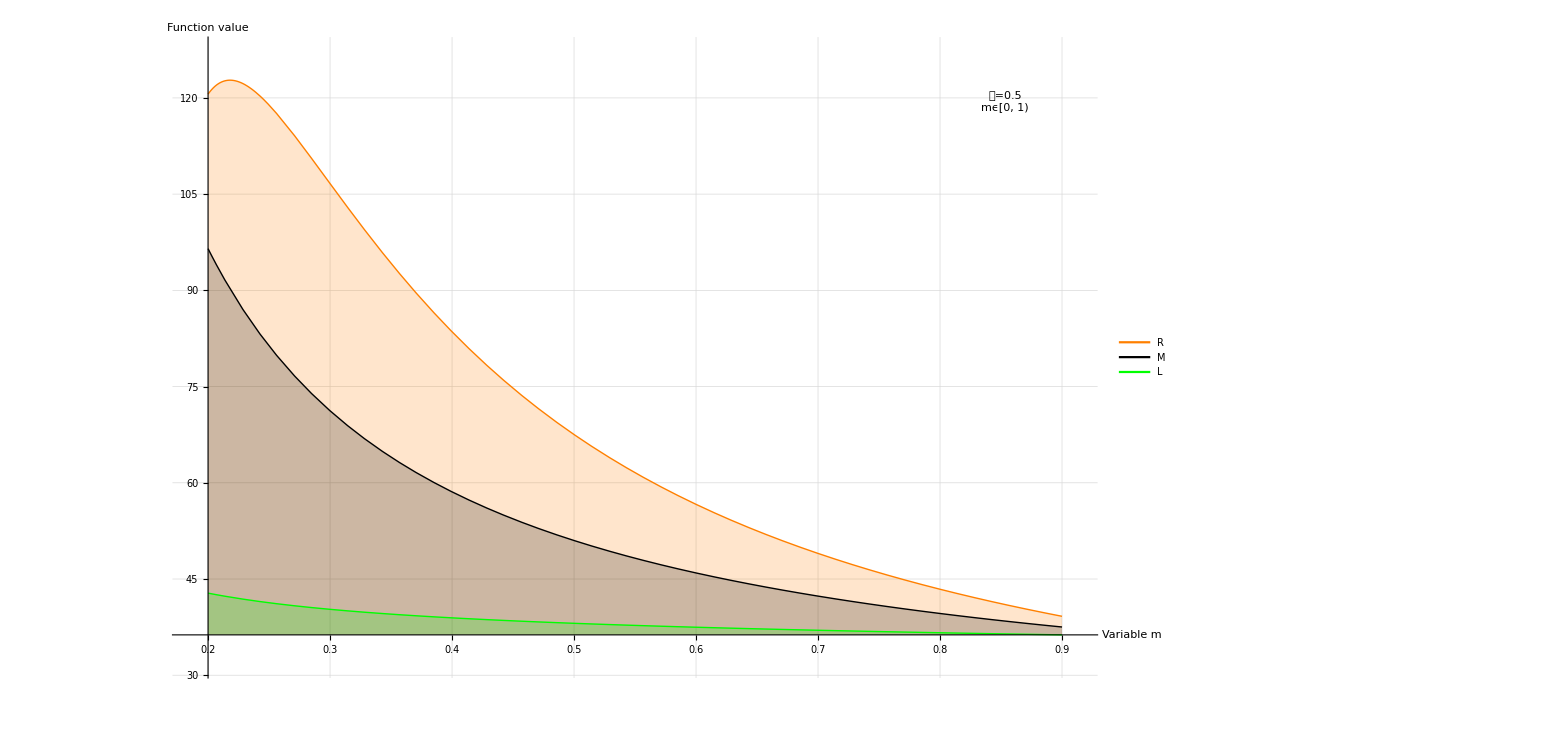

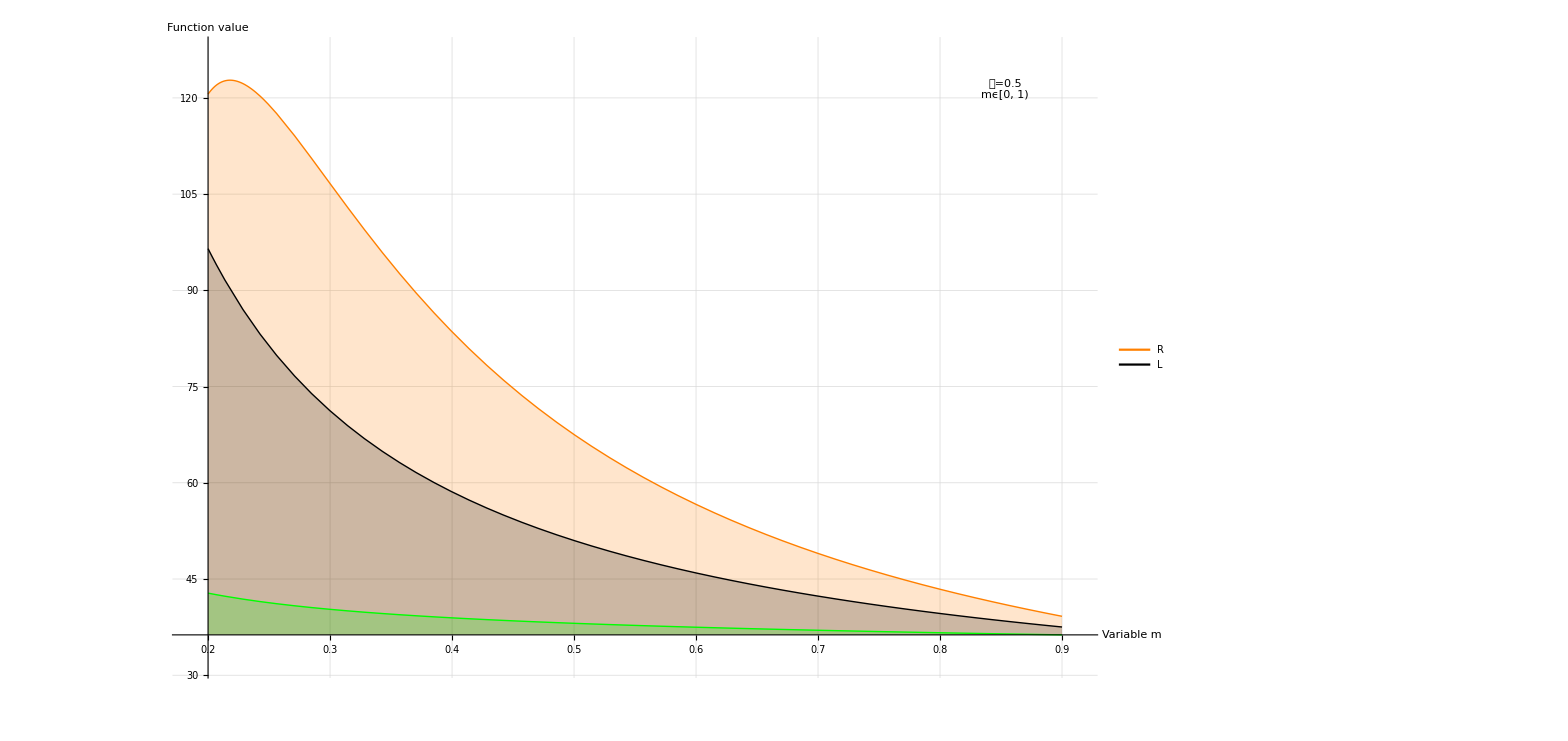

```mathematica
Integrate[0.5(6-x)^(-0.5)(11-(1+m)x)/(2m)(1+(11-(1+m)x)/(2m)),{x,5,5.5}]
```

-2.31903+2.41045/m^2-1.16839/m+1.25981 m

```mathematica
Integrate[0.5(m^0.5)(x-(5/m))^(-0.5)((11-(1+m)x)/(2m))(1+(11-(1+m)x)/(2m)),{x,5/m,5.5/m}]
```

ConditionalExpression[(0.125 (37.7831-85.1828 m+33.5404 m^2+16.4992 m^3))/m^4.,Re[m]>0&&Im[m]==0]

```mathematica
Integrate[(0.5/2)((6-x)^(-0.5)(x)(1+x)),{x,5,6}]
```

18.9333

```mathematica
Integrate[(0.5/2)(m^0.5)((x-5/m)^(-0.5)(x)(1+x)),{x,5/m,6/m}]
```

ConditionalExpression[(0.25 (57.0667+10.6667 m))/m^2.,Re[m]>0&&Im[m]==0]

```mathematica
Integrate[(0.5(0.5))(6-x)^(-0.5)((6-x)((((x-5)(6-5m))/m)(1+(((x-5)(6-5m))/m)))+m(x-5)(((((6-x)(6-5m))/m)(1+(((6-x)(6-5m))/m))))+m(x-5)(((((6-x)(6-5m))/m^2)(1+(((6-x)(6-5m))/m^2))))+m^2(6-x)(((((x-5)(6-5m))/m^2)(1+(((x-5)(6-5m))/m^2))))),{x,5,6}]
```

0.32381+1.02857/m^3+1.02857/m^2-2.02857/m+0.047619 m

```mathematica
Plot[{((0.5(0.1))/((2)(1.5)))+(m/(2(1.5)))((6/m)(1+6/m)+(5/m)(1+5/m)+0.5(m)(6/m^2(1+6/m^2)))-(0.32380952381661327+1.028571428568833/m^3+1.0285714285770597/m^2-2.028571428580843/m+0.047619047617670655 m),(5)(6)+2.3190279344205718+2.4104492906578976/m-1.1683936140394326/m-1.2598149702767585 m+(0.125 (37.783072341401216-85.18279690693952 m+33.54043165428191 m^2+16.49915822768612 m))/1,1.933333333333334+(0.25 (7.06666666666666+10.666666666666666 m))/m},{m,0.2,0.9},PlotStyle->{{Orange,Thick},{Black,Thick}, {Green,Thick}},PlotLegends->Placed[{Style["R",FontSize->40],Style["M",FontSize->40],Style["L",FontSize->40]},{0.9,0.9}],AxesLabel->{Style["Variable m",FontSize->30],Style["Function value",FontSize->30]},ImageSize->1200,(*ensures at least 1000px wide*)GridLines->Automatic,LabelStyle->Directive[Black,30],Filling->Axis,Epilog->Inset[Framed[Column[{Style["mϵ(0.2, 0.9)",Black,28]}],RoundingRadius->5],Scaled[{0.9,0.9}]]]
```